```mathematica
data=Transpose[Import["C:\\Users\\Abigail\\Desktop\\Wolfram data\\Nematode\\Clade one\\Mt genes\\Nematode clade one mt genes.csv"]];
hdr=data//First
```

{Classification,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus}

```mathematica
Dimensions[data]
```

{7,79}

```mathematica
nematode12S=data[[2,2;;79]]
nematode16S=data[[3,2;;79]]
nematodeCOI=data[[4,2;;79]]
nematodeCOII=data[[5,2;;79]]
nematodecytb=data[[6,2;;79]]
nematodeND=data[[7,2;;79]]
```

{0.147,0.187,0.196,0.225,0.173,0.179,0.17,0.086,0.193,0.21,0.023,0.032,0.026,0.075,0.078,0.029,0.078,0.032,0.014,0.069,0.072,0.029,0.078,0.023,0.089,0.081,0.009,0.098,0.072,0.075,0.026,0.081,0.061,0.081,0.009,0.072,0.069,0.089,0.282,0.28,0.285,0.282,0.297,0.308,0.285,0.305,0.271,0.271,0.259,0.271,0.294,0.297,0.265,0.297,0.282,0.285,0.28,0.285,0.314,0.308,0.285,0.32,0.282,0.288,0.277,0.282,0.305,0.311,0.282,0.311,0.262,0.268,0.265,0.265,0.3,0.303,0.265,0.305}

{0.225,0.262,0.253,0.262,0.24,0.242,0.237,0.101,0.247,0.232,0.048,0.036,0.041,0.108,0.113,0.038,0.101,0.048,0.053,0.104,0.096,0.05,0.104,0.043,0.098,0.109,0.023,0.098,0.098,0.118,0.043,0.091,0.088,0.106,0.025,0.111,0.089,0.099,0.285,0.27,0.265,0.272,0.3,0.278,0.272,0.3,0.296,0.291,0.286,0.295,0.298,0.293,0.29,0.298,0.308,0.306,0.303,0.311,0.301,0.311,0.305,0.296,0.288,0.288,0.286,0.301,0.3,0.296,0.29,0.3,0.29,0.281,0.286,0.296,0.296,0.286,0.288,0.291}

{0.243,0.266,0.262,0.262,0.253,0.26,0.243,0.174,0.257,0.256,0.092,0.097,0.088,0.129,0.155,0.079,0.143,0.105,0.091,0.126,0.131,0.104,0.139,0.096,0.116,0.15,0.067,0.135,0.121,0.159,0.094,0.137,0.131,0.124,0.083,0.142,0.128,0.14,0.298,0.292,0.292,0.307,0.296,0.298,0.294,0.3,0.294,0.296,0.28,0.292,0.29,0.291,0.286,0.287,0.315,0.32,0.306,0.311,0.309,0.319,0.305,0.321,0.308,0.311,0.312,0.313,0.305,0.313,0.313,0.316,0.3,0.293,0.298,0.307,0.292,0.299,0.299,0.298}

{0.304,0.286,0.295,0.313,0.283,0.295,0.319,0.208,0.281,0.293,0.096,0.085,0.092,0.132,0.161,0.076,0.13,0.089,0.083,0.121,0.152,0.082,0.12,0.069,0.143,0.17,0.067,0.149,0.145,0.158,0.085,0.147,0.143,0.12,0.072,0.165,0.13,0.143,0.428,0.409,0.42,0.42,0.408,0.411,0.413,0.426,0.391,0.388,0.399,0.38,0.397,0.391,0.382,0.397,0.384,0.373,0.388,0.373,0.373,0.382,0.375,0.389,0.4,0.393,0.393,0.382,0.422,0.409,0.408,0.418,0.375,0.379,0.38,0.371,0.404,0.371,0.373,0.402}

{0.275,0.281,0.293,0.283,0.255,0.284,0.297,0.21,0.28,0.266,0.096,0.077,0.091,0.147,0.169,0.081,0.145,0.094,0.082,0.134,0.167,0.084,0.143,0.103,0.141,0.164,0.062,0.139,0.15,0.154,0.093,0.14,0.152,0.146,0.075,0.172,0.156,0.149,0.372,0.371,0.357,0.358,0.365,0.354,0.363,0.368,0.366,0.364,0.355,0.352,0.363,0.359,0.366,0.369,0.349,0.337,0.333,0.329,0.345,0.341,0.338,0.354,0.35,0.346,0.351,0.339,0.361,0.339,0.354,0.357,0.349,0.35,0.349,0.352,0.356,0.349,0.346,0.357}

{0.301,0.331,0.335,0.339,0.296,0.294,0.292,0.236,0.31,0.306,0.095,0.094,0.109,0.154,0.162,0.076,0.147,0.103,0.091,0.157,0.17,0.1,0.154,0.112,0.155,0.178,0.079,0.164,0.145,0.16,0.112,0.148,0.132,0.152,0.057,0.162,0.14,0.164,0.398,0.41,0.409,0.423,0.424,0.416,0.406,0.414,0.387,0.393,0.401,0.405,0.4,0.401,0.386,0.406,0.411,0.414,0.414,0.41,0.419,0.423,0.414,0.421,0.414,0.424,0.411,0.426,0.415,0.42,0.401,0.419,0.383,0.385,0.391,0.383,0.385,0.401,0.376,0.393}

```mathematica
Stat[clusterdata_]:={Mean[#],StandardDeviation[#],MinMax[#]}&/@clusterdata
```

```mathematica
PlotCluster[clusterdata_,plotlabel_]:=ListPlot[clusterdata,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},Frame->True,FrameLabel->{"Samples","Genetic Distance"},GridLines->Automatic,ImageSize->Medium,PlotStyle->{{PointSize[Medium],Red},{PointSize[Medium],Green},{PointSize[Medium],Blue},{PointSize[Medium],Orange}},PlotLabel->plotlabel]
```

```mathematica
{clstrnematode12S,clstrnematode16S,clstrnematodeCOI,clstrnematodeCOII,clstrnematodecytb,clstrnematodeND}=FindClusters[#,2,Method->"KMeans"]&/@{nematode12S,nematode16S,nematodeCOI,nematodeCOII,nematodecytb,nematodeND};
```

```mathematica
statdata=Stat/@{clstrnematode12S,clstrnematode16S,clstrnematodeCOI,clstrnematodeCOII,clstrnematodecytb,clstrnematodeND}
```

{{{0.0601,0.0324668,{0.009,0.147}},{0.271083,0.0395506,{0.17,0.32}}},{{0.283531,0.0217841,{0.225,0.311}},{0.0786207,0.0313613,{0.023,0.118}}},{{0.293429,0.0205639,{0.243,0.321}},{0.119862,0.0267765,{0.067,0.174}}},{{0.376449,0.0416298,{0.281,0.428}},{0.121828,0.036685,{0.067,0.208}}},{{0.339735,0.0309386,{0.255,0.372}},{0.128138,0.037423,{0.062,0.21}}},{{0.38849,0.0396217,{0.292,0.426}},{0.134759,0.038397,{0.057,0.236}}}}

```mathematica
MySort[clusterdata_]:=Module[{len,max,or},
len=Length@clusterdata;
max=Max/@clusterdata;
or=Ordering[max];
clusterdata[[or]]
];
```

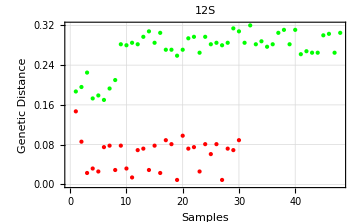

```mathematica
PlotCluster[MySort[clstrnematode12S],"12S"]
```

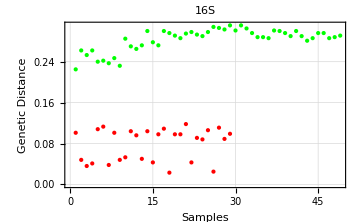

```mathematica
PlotCluster[MySort[clstrnematode16S],"16S"]
```

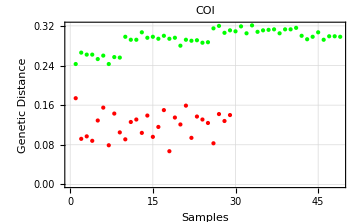

```mathematica
PlotCluster[MySort[clstrnematodeCOI],"COI"]
```

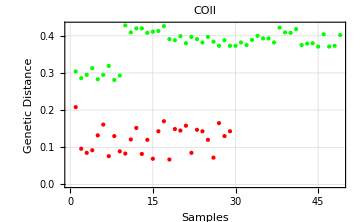

```mathematica
PlotCluster[MySort[clstrnematodeCOII],"COII"]
```

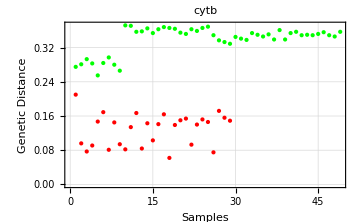

```mathematica
PlotCluster[MySort[clstrnematodecytb],"cytb"]
```

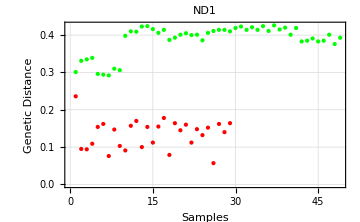

```mathematica
PlotCluster[MySort[clstrnematodeND],"ND1"]
```

```mathematica
FindClusters[nematode12S,2,Method->"KMeans"]
```

{{0.147,0.086,0.023,0.032,0.026,0.075,0.078,0.029,0.078,0.032,0.014,0.069,0.072,0.029,0.078,0.023,0.089,0.081,0.009,0.098,0.072,0.075,0.026,0.081,0.061,0.081,0.009,0.072,0.069,0.089},{0.187,0.196,0.225,0.173,0.179,0.17,0.193,0.21,0.282,0.28,0.285,0.282,0.297,0.308,0.285,0.305,0.271,0.271,0.259,0.271,0.294,0.297,0.265,0.297,0.282,0.285,0.28,0.285,0.314,0.308,0.285,0.32,0.282,0.288,0.277,0.282,0.305,0.311,0.282,0.311,0.262,0.268,0.265,0.265,0.3,0.303,0.265,0.305}}

```mathematica
Mean[nematode12S]
```

0.189936

```mathematica
Mean[{0.147,0.086,0.023,0.032,0.026,0.075,0.078,0.029,0.078,0.032,0.014,0.069,0.072,0.029,0.078,0.023,0.089,0.081,0.009,0.098,0.072,0.075,0.026,0.081,0.061,0.081,0.009,0.072,0.069,0.089}]
```

0.0601

```mathematica
StandardDeviation[{0.147,0.086,0.023,0.032,0.026,0.075,0.078,0.029,0.078,0.032,0.014,0.069,0.072,0.029,0.078,0.023,0.089,0.081,0.009,0.098,0.072,0.075,0.026,0.081,0.061,0.081,0.009,0.072,0.069,0.089}]
```

0.0324668

```mathematica
MinMax[{0.147,0.086,0.023,0.032,0.026,0.075,0.078,0.029,0.078,0.032,0.014,0.069,0.072,0.029,0.078,0.023,0.089,0.081,0.009,0.098,0.072,0.075,0.026,0.081,0.061,0.081,0.009,0.072,0.069,0.089}]
```

{0.009,0.147}

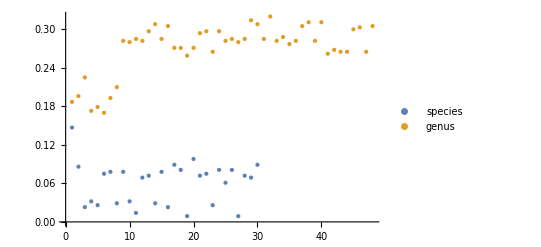

```mathematica
ListPlot[FindClusters[nematode12S,2,Method->"KMeans"],PlotLegends->{species, genus},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.187,0.196,0.225,0.173,0.179,0.17,0.193,0.21,0.282,0.28,0.285,0.282,0.297,0.308,0.285,0.305,0.271,0.271,0.259,0.271,0.294,0.297,0.265,0.297,0.282,0.285,0.28,0.285,0.314,0.308,0.285,0.32,0.282,0.288,0.277,0.282,0.305,0.311,0.282,0.311,0.262,0.268,0.265,0.265,0.3,0.303,0.265,0.305}]
```

0.271083

```mathematica
StandardDeviation[{0.187,0.196,0.225,0.173,0.179,0.17,0.193,0.21,0.282,0.28,0.285,0.282,0.297,0.308,0.285,0.305,0.271,0.271,0.259,0.271,0.294,0.297,0.265,0.297,0.282,0.285,0.28,0.285,0.314,0.308,0.285,0.32,0.282,0.288,0.277,0.282,0.305,0.311,0.282,0.311,0.262,0.268,0.265,0.265,0.3,0.303,0.265,0.305}]
```

0.0395506

```mathematica
MinMax[{0.187,0.196,0.225,0.173,0.179,0.17,0.193,0.21,0.282,0.28,0.285,0.282,0.297,0.308,0.285,0.305,0.271,0.271,0.259,0.271,0.294,0.297,0.265,0.297,0.282,0.285,0.28,0.285,0.314,0.308,0.285,0.32,0.282,0.288,0.277,0.282,0.305,0.311,0.282,0.311,0.262,0.268,0.265,0.265,0.3,0.303,0.265,0.305}]
```

{0.17,0.32}

```mathematica
FindClusters[nematode16S,2,Method->"KMeans"]
```

{{0.225,0.262,0.253,0.262,0.24,0.242,0.237,0.247,0.232,0.285,0.27,0.265,0.272,0.3,0.278,0.272,0.3,0.296,0.291,0.286,0.295,0.298,0.293,0.29,0.298,0.308,0.306,0.303,0.311,0.301,0.311,0.305,0.296,0.288,0.288,0.286,0.301,0.3,0.296,0.29,0.3,0.29,0.281,0.286,0.296,0.296,0.286,0.288,0.291},{0.101,0.048,0.036,0.041,0.108,0.113,0.038,0.101,0.048,0.053,0.104,0.096,0.05,0.104,0.043,0.098,0.109,0.023,0.098,0.098,0.118,0.043,0.091,0.088,0.106,0.025,0.111,0.089,0.099}}

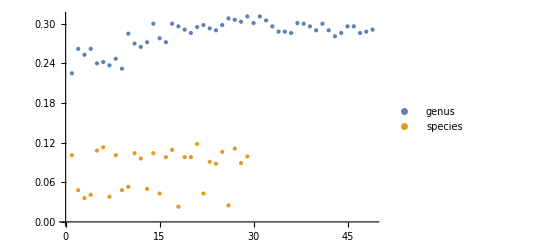

```mathematica
ListPlot[FindClusters[nematode16S,2,Method->"KMeans"],PlotLegends->{genus, species},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.101,0.048,0.036,0.041,0.108,0.113,0.038,0.101,0.048,0.053,0.104,0.096,0.05,0.104,0.043,0.098,0.109,0.023,0.098,0.098,0.118,0.043,0.091,0.088,0.106,0.025,0.111,0.089,0.099}]
```

0.0786207

```mathematica
StandardDeviation[{0.101,0.048,0.036,0.041,0.108,0.113,0.038,0.101,0.048,0.053,0.104,0.096,0.05,0.104,0.043,0.098,0.109,0.023,0.098,0.098,0.118,0.043,0.091,0.088,0.106,0.025,0.111,0.089,0.099}]
```

0.0313613

```mathematica
MinMax[{0.101,0.048,0.036,0.041,0.108,0.113,0.038,0.101,0.048,0.053,0.104,0.096,0.05,0.104,0.043,0.098,0.109,0.023,0.098,0.098,0.118,0.043,0.091,0.088,0.106,0.025,0.111,0.089,0.099}]
```

{0.023,0.118}

```mathematica
Mean[{0.225,0.262,0.253,0.262,0.24,0.242,0.237,0.247,0.232,0.285,0.27,0.265,0.272,0.3,0.278,0.272,0.3,0.296,0.291,0.286,0.295,0.298,0.293,0.29,0.298,0.308,0.306,0.303,0.311,0.301,0.311,0.305,0.296,0.288,0.288,0.286,0.301,0.3,0.296,0.29,0.3,0.29,0.281,0.286,0.296,0.296,0.286,0.288,0.291}]
```

0.283531

```mathematica
StandardDeviation[{0.225,0.262,0.253,0.262,0.24,0.242,0.237,0.247,0.232,0.285,0.27,0.265,0.272,0.3,0.278,0.272,0.3,0.296,0.291,0.286,0.295,0.298,0.293,0.29,0.298,0.308,0.306,0.303,0.311,0.301,0.311,0.305,0.296,0.288,0.288,0.286,0.301,0.3,0.296,0.29,0.3,0.29,0.281,0.286,0.296,0.296,0.286,0.288,0.291}]
```

0.0217841

```mathematica
MinMax[{0.225,0.262,0.253,0.262,0.24,0.242,0.237,0.247,0.232,0.285,0.27,0.265,0.272,0.3,0.278,0.272,0.3,0.296,0.291,0.286,0.295,0.298,0.293,0.29,0.298,0.308,0.306,0.303,0.311,0.301,0.311,0.305,0.296,0.288,0.288,0.286,0.301,0.3,0.296,0.29,0.3,0.29,0.281,0.286,0.296,0.296,0.286,0.288,0.291}]
```

{0.225,0.311}

```mathematica
FindClusters[nematodeCOI,2,Method->"KMeans"]
```

{{0.243,0.266,0.262,0.262,0.253,0.26,0.243,0.257,0.256,0.298,0.292,0.292,0.307,0.296,0.298,0.294,0.3,0.294,0.296,0.28,0.292,0.29,0.291,0.286,0.287,0.315,0.32,0.306,0.311,0.309,0.319,0.305,0.321,0.308,0.311,0.312,0.313,0.305,0.313,0.313,0.316,0.3,0.293,0.298,0.307,0.292,0.299,0.299,0.298},{0.174,0.092,0.097,0.088,0.129,0.155,0.079,0.143,0.105,0.091,0.126,0.131,0.104,0.139,0.096,0.116,0.15,0.067,0.135,0.121,0.159,0.094,0.137,0.131,0.124,0.083,0.142,0.128,0.14}}

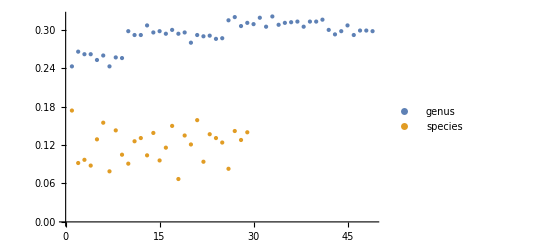

```mathematica
ListPlot[FindClusters[nematodeCOI,2,Method->"KMeans"],PlotLegends->{genus,species},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.174,0.092,0.097,0.088,0.129,0.155,0.079,0.143,0.105,0.091,0.126,0.131,0.104,0.139,0.096,0.116,0.15,0.067,0.135,0.121,0.159,0.094,0.137,0.131,0.124,0.083,0.142,0.128,0.14}]
```

0.119862

```mathematica
StandardDeviation[{0.174,0.092,0.097,0.088,0.129,0.155,0.079,0.143,0.105,0.091,0.126,0.131,0.104,0.139,0.096,0.116,0.15,0.067,0.135,0.121,0.159,0.094,0.137,0.131,0.124,0.083,0.142,0.128,0.14}]
```

0.0267765

```mathematica
MinMax[{0.174,0.092,0.097,0.088,0.129,0.155,0.079,0.143,0.105,0.091,0.126,0.131,0.104,0.139,0.096,0.116,0.15,0.067,0.135,0.121,0.159,0.094,0.137,0.131,0.124,0.083,0.142,0.128,0.14}]
```

{0.067,0.174}

```mathematica
Mean[{0.243,0.266,0.262,0.262,0.253,0.26,0.243,0.257,0.256,0.298,0.292,0.292,0.307,0.296,0.298,0.294,0.3,0.294,0.296,0.28,0.292,0.29,0.291,0.286,0.287,0.315,0.32,0.306,0.311,0.309,0.319,0.305,0.321,0.308,0.311,0.312,0.313,0.305,0.313,0.313,0.316,0.3,0.293,0.298,0.307,0.292,0.299,0.299,0.298}]
```

0.293429

```mathematica
StandardDeviation[{0.243,0.266,0.262,0.262,0.253,0.26,0.243,0.257,0.256,0.298,0.292,0.292,0.307,0.296,0.298,0.294,0.3,0.294,0.296,0.28,0.292,0.29,0.291,0.286,0.287,0.315,0.32,0.306,0.311,0.309,0.319,0.305,0.321,0.308,0.311,0.312,0.313,0.305,0.313,0.313,0.316,0.3,0.293,0.298,0.307,0.292,0.299,0.299,0.298}]
```

0.0205639

```mathematica
MinMax[{0.243,0.266,0.262,0.262,0.253,0.26,0.243,0.257,0.256,0.298,0.292,0.292,0.307,0.296,0.298,0.294,0.3,0.294,0.296,0.28,0.292,0.29,0.291,0.286,0.287,0.315,0.32,0.306,0.311,0.309,0.319,0.305,0.321,0.308,0.311,0.312,0.313,0.305,0.313,0.313,0.316,0.3,0.293,0.298,0.307,0.292,0.299,0.299,0.298}]
```

{0.243,0.321}

```mathematica
FindClusters[nematodeCOII,2,Method->"KMeans"]
```

{{0.304,0.286,0.295,0.313,0.283,0.295,0.319,0.281,0.293,0.428,0.409,0.42,0.42,0.408,0.411,0.413,0.426,0.391,0.388,0.399,0.38,0.397,0.391,0.382,0.397,0.384,0.373,0.388,0.373,0.373,0.382,0.375,0.389,0.4,0.393,0.393,0.382,0.422,0.409,0.408,0.418,0.375,0.379,0.38,0.371,0.404,0.371,0.373,0.402},{0.208,0.096,0.085,0.092,0.132,0.161,0.076,0.13,0.089,0.083,0.121,0.152,0.082,0.12,0.069,0.143,0.17,0.067,0.149,0.145,0.158,0.085,0.147,0.143,0.12,0.072,0.165,0.13,0.143}}

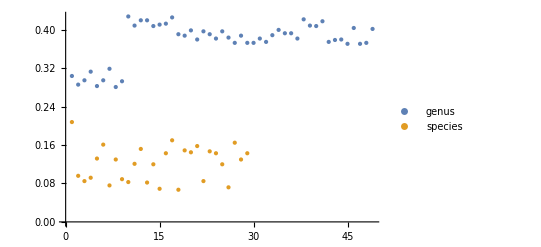

```mathematica
ListPlot[FindClusters[nematodeCOII,2,Method->"KMeans"],PlotLegends->{genus,species},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.208,0.096,0.085,0.092,0.132,0.161,0.076,0.13,0.089,0.083,0.121,0.152,0.082,0.12,0.069,0.143,0.17,0.067,0.149,0.145,0.158,0.085,0.147,0.143,0.12,0.072,0.165,0.13,0.143}]
```

0.121828

```mathematica
StandardDeviation[{0.208,0.096,0.085,0.092,0.132,0.161,0.076,0.13,0.089,0.083,0.121,0.152,0.082,0.12,0.069,0.143,0.17,0.067,0.149,0.145,0.158,0.085,0.147,0.143,0.12,0.072,0.165,0.13,0.143}]
```

0.036685

```mathematica
MinMax[{0.208,0.096,0.085,0.092,0.132,0.161,0.076,0.13,0.089,0.083,0.121,0.152,0.082,0.12,0.069,0.143,0.17,0.067,0.149,0.145,0.158,0.085,0.147,0.143,0.12,0.072,0.165,0.13,0.143}]
```

{0.067,0.208}

```mathematica
Mean[{0.304,0.286,0.295,0.313,0.283,0.295,0.319,0.281,0.293,0.428,0.409,0.42,0.42,0.408,0.411,0.413,0.426,0.391,0.388,0.399,0.38,0.397,0.391,0.382,0.397,0.384,0.373,0.388,0.373,0.373,0.382,0.375,0.389,0.4,0.393,0.393,0.382,0.422,0.409,0.408,0.418,0.375,0.379,0.38,0.371,0.404,0.371,0.373,0.402}]
```

0.376449

```mathematica
StandardDeviation[{0.304,0.286,0.295,0.313,0.283,0.295,0.319,0.281,0.293,0.428,0.409,0.42,0.42,0.408,0.411,0.413,0.426,0.391,0.388,0.399,0.38,0.397,0.391,0.382,0.397,0.384,0.373,0.388,0.373,0.373,0.382,0.375,0.389,0.4,0.393,0.393,0.382,0.422,0.409,0.408,0.418,0.375,0.379,0.38,0.371,0.404,0.371,0.373,0.402}]
```

0.0416298

```mathematica
MinMax[{0.304,0.286,0.295,0.313,0.283,0.295,0.319,0.281,0.293,0.428,0.409,0.42,0.42,0.408,0.411,0.413,0.426,0.391,0.388,0.399,0.38,0.397,0.391,0.382,0.397,0.384,0.373,0.388,0.373,0.373,0.382,0.375,0.389,0.4,0.393,0.393,0.382,0.422,0.409,0.408,0.418,0.375,0.379,0.38,0.371,0.404,0.371,0.373,0.402}]
```

{0.281,0.428}

```mathematica
FindClusters[nematodecytb,2,Method->"KMeans"]
```

{{0.275,0.281,0.293,0.283,0.255,0.284,0.297,0.28,0.266,0.372,0.371,0.357,0.358,0.365,0.354,0.363,0.368,0.366,0.364,0.355,0.352,0.363,0.359,0.366,0.369,0.349,0.337,0.333,0.329,0.345,0.341,0.338,0.354,0.35,0.346,0.351,0.339,0.361,0.339,0.354,0.357,0.349,0.35,0.349,0.352,0.356,0.349,0.346,0.357},{0.21,0.096,0.077,0.091,0.147,0.169,0.081,0.145,0.094,0.082,0.134,0.167,0.084,0.143,0.103,0.141,0.164,0.062,0.139,0.15,0.154,0.093,0.14,0.152,0.146,0.075,0.172,0.156,0.149}}

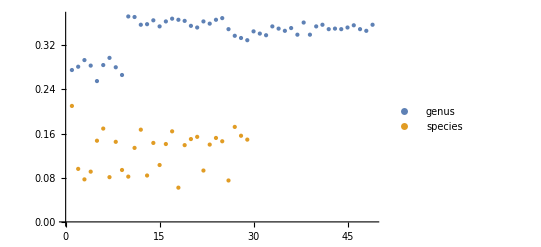

```mathematica
ListPlot[FindClusters[nematodecytb,2,Method->"KMeans"],PlotLegends->{genus,species},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.21,0.096,0.077,0.091,0.147,0.169,0.081,0.145,0.094,0.082,0.134,0.167,0.084,0.143,0.103,0.141,0.164,0.062,0.139,0.15,0.154,0.093,0.14,0.152,0.146,0.075,0.172,0.156,0.149}]
```

0.128138

```mathematica
StandardDeviation[{0.21,0.096,0.077,0.091,0.147,0.169,0.081,0.145,0.094,0.082,0.134,0.167,0.084,0.143,0.103,0.141,0.164,0.062,0.139,0.15,0.154,0.093,0.14,0.152,0.146,0.075,0.172,0.156,0.149}]
```

0.037423

```mathematica
MinMax[{0.21,0.096,0.077,0.091,0.147,0.169,0.081,0.145,0.094,0.082,0.134,0.167,0.084,0.143,0.103,0.141,0.164,0.062,0.139,0.15,0.154,0.093,0.14,0.152,0.146,0.075,0.172,0.156,0.149}]
```

{0.062,0.21}

```mathematica
Mean[{0.275,0.281,0.293,0.283,0.255,0.284,0.297,0.28,0.266,0.372,0.371,0.357,0.358,0.365,0.354,0.363,0.368,0.366,0.364,0.355,0.352,0.363,0.359,0.366,0.369,0.349,0.337,0.333,0.329,0.345,0.341,0.338,0.354,0.35,0.346,0.351,0.339,0.361,0.339,0.354,0.357,0.349,0.35,0.349,0.352,0.356,0.349,0.346,0.357}]
```

0.339735

```mathematica
StandardDeviation[{0.275,0.281,0.293,0.283,0.255,0.284,0.297,0.28,0.266,0.372,0.371,0.357,0.358,0.365,0.354,0.363,0.368,0.366,0.364,0.355,0.352,0.363,0.359,0.366,0.369,0.349,0.337,0.333,0.329,0.345,0.341,0.338,0.354,0.35,0.346,0.351,0.339,0.361,0.339,0.354,0.357,0.349,0.35,0.349,0.352,0.356,0.349,0.346,0.357}]
```

0.0309386

```mathematica
MinMax[{0.275,0.281,0.293,0.283,0.255,0.284,0.297,0.28,0.266,0.372,0.371,0.357,0.358,0.365,0.354,0.363,0.368,0.366,0.364,0.355,0.352,0.363,0.359,0.366,0.369,0.349,0.337,0.333,0.329,0.345,0.341,0.338,0.354,0.35,0.346,0.351,0.339,0.361,0.339,0.354,0.357,0.349,0.35,0.349,0.352,0.356,0.349,0.346,0.357}]
```

{0.255,0.372}

```mathematica
FindClusters[nematodeND,2,Method->"KMeans"]
```

{{0.301,0.331,0.335,0.339,0.296,0.294,0.292,0.31,0.306,0.398,0.41,0.409,0.423,0.424,0.416,0.406,0.414,0.387,0.393,0.401,0.405,0.4,0.401,0.386,0.406,0.411,0.414,0.414,0.41,0.419,0.423,0.414,0.421,0.414,0.424,0.411,0.426,0.415,0.42,0.401,0.419,0.383,0.385,0.391,0.383,0.385,0.401,0.376,0.393},{0.236,0.095,0.094,0.109,0.154,0.162,0.076,0.147,0.103,0.091,0.157,0.17,0.1,0.154,0.112,0.155,0.178,0.079,0.164,0.145,0.16,0.112,0.148,0.132,0.152,0.057,0.162,0.14,0.164}}

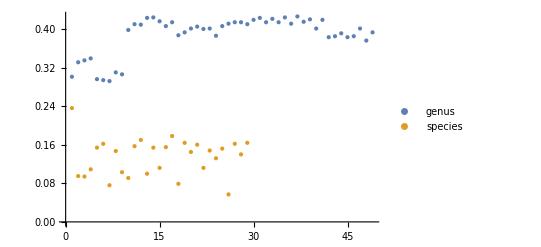

```mathematica
ListPlot[FindClusters[nematodeND,2,Method->"KMeans"],PlotLegends->{genus,species},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.236,0.095,0.094,0.109,0.154,0.162,0.076,0.147,0.103,0.091,0.157,0.17,0.1,0.154,0.112,0.155,0.178,0.079,0.164,0.145,0.16,0.112,0.148,0.132,0.152,0.057,0.162,0.14,0.164}]
```

0.134759

```mathematica
StandardDeviation[{0.236,0.095,0.094,0.109,0.154,0.162,0.076,0.147,0.103,0.091,0.157,0.17,0.1,0.154,0.112,0.155,0.178,0.079,0.164,0.145,0.16,0.112,0.148,0.132,0.152,0.057,0.162,0.14,0.164}]
```

0.038397

```mathematica
MinMax[{0.236,0.095,0.094,0.109,0.154,0.162,0.076,0.147,0.103,0.091,0.157,0.17,0.1,0.154,0.112,0.155,0.178,0.079,0.164,0.145,0.16,0.112,0.148,0.132,0.152,0.057,0.162,0.14,0.164}]
```

{0.057,0.236}

```mathematica
Mean[{0.301,0.331,0.335,0.339,0.296,0.294,0.292,0.31,0.306,0.398,0.41,0.409,0.423,0.424,0.416,0.406,0.414,0.387,0.393,0.401,0.405,0.4,0.401,0.386,0.406,0.411,0.414,0.414,0.41,0.419,0.423,0.414,0.421,0.414,0.424,0.411,0.426,0.415,0.42,0.401,0.419,0.383,0.385,0.391,0.383,0.385,0.401,0.376,0.393}]
```

0.38849

```mathematica
StandardDeviation[{0.301,0.331,0.335,0.339,0.296,0.294,0.292,0.31,0.306,0.398,0.41,0.409,0.423,0.424,0.416,0.406,0.414,0.387,0.393,0.401,0.405,0.4,0.401,0.386,0.406,0.411,0.414,0.414,0.41,0.419,0.423,0.414,0.421,0.414,0.424,0.411,0.426,0.415,0.42,0.401,0.419,0.383,0.385,0.391,0.383,0.385,0.401,0.376,0.393}]
```

0.0396217

```mathematica
MinMax[{0.301,0.331,0.335,0.339,0.296,0.294,0.292,0.31,0.306,0.398,0.41,0.409,0.423,0.424,0.416,0.406,0.414,0.387,0.393,0.401,0.405,0.4,0.401,0.386,0.406,0.411,0.414,0.414,0.41,0.419,0.423,0.414,0.421,0.414,0.424,0.411,0.426,0.415,0.42,0.401,0.419,0.383,0.385,0.391,0.383,0.385,0.401,0.376,0.393}]
```

{0.292,0.426}